# Rovibrational Spectroscopy of Diatomic Molecules using Nikiforov-Uvarov Functional Analysis

## Results

## Symbols and Data

DO NOT run this cell (defining symbols) twice in the same notebook session. It will throw an error. If you want to evaluate the entire notebook, quit the kernel first.

```mathematica
(*Define subscripted symbols*)
Notation`AutoLoadNotationPalette=False;
<<Notation`;
Symbolize/@{Subscript[D, e],Subscript[r, e],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[E, 𝓃ℓ],Subscript[ψ, 𝓃ℓ]};
<<SciDraw`;
```

```mathematica
(*Importing Dataset of Spectroscopic Constants*)
SetDirectory[NotebookDirectory[]];
molecularData=Import["data/molecular_data.csv", {"CSV","Dataset"},"HeaderLines"->{1,1}]
```

## Parameters and Functions

```mathematica
ℏ=1973.269804;
moleculesList = {"H2", "LiH", "HCl", "CO", "VH", "CrH", "CuLi", "TiC", "NiC", "ScN"};
(*function to get spectroscopic data for a chosen molecule*)
chooseMolecule[molecule_]:=({Subscript[D, e],Subscript[r, e],μ,α}={"D_e","r_e","mu","alpha"}/.Normal[molecularData[molecule]];μ=μ*9.3149410372*10^8; (*amu to eV/c^2*))

(*NUFA Definitions*)
β:=(2μ Subscript[r, e]^2)/(α^2 ℏ^2);
Subscript[X, 1]:=Subscript[D, e]+(ℓ(ℓ+1))/(α^2 β)(3/α^2-1/α);
Subscript[X, 2]:=-2 Subscript[D, e]+(ℓ(ℓ+1))/(α^2 β)(-6/α^2+4/α);
Subscript[X, 3]:=(ℓ(ℓ+1))/(α^2 β)(1+3/α^2-3/α);
λ:=√(β Subscript[X, 1]);
ν:=√(β (-Subscript[E, 𝓃ℓ]+Subscript[X, 3]));

(*Energy Equation*)
Subscript[E, 𝓃ℓ]:=Subscript[X, 3]-1/β(1/2+𝓃+Subscript[X, 2]/2 √(β/Subscript[X, 1]))^2;

nonNormalizedEigenfunction[r_]:=FullSimplify[(ⅇ^(-λ z)z^ν Hypergeometric1F1[-𝓃,(1+2ν),2λ z])/.{z->ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])}];
(*Normalization Constant*)
𝒩:=NIntegrate[(nonNormalizedEigenfunction[r])^2,{r,0,∞}];
(*Normalized Eigenfunction*)
Subscript[ψ, 𝓃ℓ][r_]:=FullSimplify[1/(√𝒩)nonNormalizedEigenfunction[r]];

(*Potential Functions*)
ModifiedMorse[r_]:=Subscript[D, e] ⅇ^(-2α(r-Subscript[r, e])/Subscript[r, e])-2 Subscript[D, e] ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])+ℏ^2/(2μ)(ℓ(ℓ+1))/r^2;
pekerisApproximated[r_]:=(Subscript[X, 1] z^2+Subscript[X, 2] z+Subscript[X, 3])/.{z->ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])};
```

## Numerical Results and Test Plots

## Eigenvalues

#### Basic Example

```mathematica
(*Calculating an Energy Eigenvalue*)
(*adjust NumberForm arguments to control precision*)
chooseMolecule["LiH"]
𝓃=7;
ℓ=10;
StringForm["Energy Eigenvalue for `` under the Modified-Morse Potential; 𝓃 = ``, ℓ = ``: `` eV",molecule,𝓃,ℓ, NumberForm[Subscript[E, 𝓃ℓ],{20,8}]]
```

Energy Eigenvalue for molecule under the Modified-Morse Potential; 𝓃 = 7, ℓ = 10: -1.29580533 eV

#### Table of Negative Eigenvalues

```mathematica
chooseMolecule["ScN"]
𝓃List ={0,1,2,3,4,5};
ℓList={0,1,2,5,10};

energyTable=Table[NumberForm[-Subscript[E, 𝓃ℓ],{20,7}],{𝓃,𝓃List},{ℓ,ℓList}];
(*column headings*)
energyTable=Prepend[%,ℓList];
(*row headings*)
energyTable=MapThread[Prepend,{%,Prepend[𝓃List,"𝓃\\ℓ"]}];
(*format to look like booktabs*)
energyTable=Grid[%,Dividers->{False,{{True,True},-1->True}},Alignment->Left,Spacings->{1,1}]

(*Table[NumberForm[-Subscript[E, 𝓃ℓ],{20,7}],{𝓃,𝓃List},{ℓ,ℓList}]//Flatten//TableForm*)
```

𝓃\ℓ | 0 | 1 | 2 | 5 | 10
0 | 4.5151043 | 4.5149796 | 4.5147301 | 4.5132332 | 4.5082446
1 | 4.4259793 | 4.4258554 | 4.4256076 | 4.4241212 | 4.4191674
2 | 4.3377427 | 4.3376196 | 4.3373736 | 4.3358976 | 4.3309786
3 | 4.2503945 | 4.2502723 | 4.2500280 | 4.2485625 | 4.2436782
4 | 4.1639347 | 4.1638134 | 4.1635709 | 4.1621157 | 4.1572662
5 | 4.0783633 | 4.0782429 | 4.0780021 | 4.0765574 | 4.0717426

## Eigenfunctions and Probability Densities

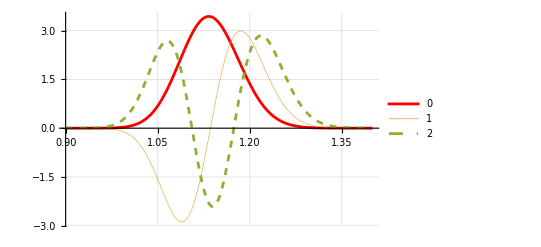

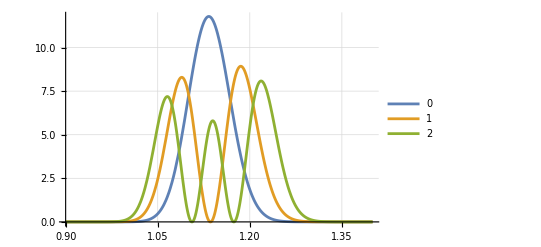

```mathematica
chooseMolecule["CO"]
ℓ=25;
Plot[Evaluate[Table[(Subscript[ψ, 𝓃ℓ][r]),{𝓃,0,2}]],{r,0.9,1.4},PlotRange->Full,PlotLegends->Range[0,2],GridLines->Automatic, PlotStyle->{Red,Thickness[0.001],Dashed}]

Plot[Evaluate[Table[(Subscript[ψ, 𝓃ℓ][r])^2,{𝓃,0,2}]],{r,0.9,1.4},PlotRange->Automatic,PlotLegends->Range[0,2],GridLines->Automatic]
```

## Plots for Publication

## 1. Potential Plots

### H_2

```mathematica
chooseMolecule["H2"];ℓ=15;
potentialPlotH2=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.92,0.92}],"H_2",FontSize->35];

(*plots*)
FigLine[
Plot[ModifiedMorse[r],{r,0.1,10},PlotRange->Full],
LineColor->Blue,LineThickness->2,LineDashing->0
];
FigLine[
Plot[pekerisApproximated[r],{r,0.1,10},PlotRange->Full],
LineColor->Red,LineThickness->2,LineDashing->8
];
},

(*plot ranges*)
XPlotRange->{0,6},XFrameLabel->textit["r (Å)"],
YPlotRange->{-5,5},YFrameLabel->textit["Potential (eV)"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,6,2,4],
YTicks->LinTicks[-4,4,2,2],

XTickLabelAllowance->23,

FontSize->25,
LineThickness->2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.8,0.2},{0.7,0.2}}
]
```

-Graphics-

### LiH

```mathematica
chooseMolecule["LiH"];ℓ=15;
potentialPlotLiH=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.9,0.92}],"LiH",FontSize->35];

(*plots*)
FigLine[
Plot[ModifiedMorse[r],{r,0.1,10},PlotRange->Full],
LineColor->Blue,LineThickness->2,LineDashing->0
];
FigLine[
Plot[pekerisApproximated[r],{r,0.1,10},PlotRange->Full],
LineColor->Red,LineThickness->2,LineDashing->8
];
},

(*plot ranges*)
XPlotRange->{0,10},XFrameLabel->textit["r (Å)"],
YPlotRange->{-3,3},YFrameLabel->textit["Potential (eV)"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,10,2,4],
YTicks->LinTicks[-4,4,2,2],

XTickLabelAllowance->23,

FontSize->25,
LineThickness->2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.8,0.2},{0.7,0.2}}
]
```

-Graphics-

### HCl

```mathematica
chooseMolecule["HCl"];ℓ=15;
potentialPlotHCl=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.89,0.92}],"HCl",FontSize->35];

(*plots*)
FigLine[
Plot[ModifiedMorse[r],{r,0.1,10},PlotRange->Full],
LineColor->Blue,LineThickness->2,LineDashing->0
];
FigLine[
Plot[pekerisApproximated[r],{r,0.1,10},PlotRange->Full],
LineColor->Red,LineThickness->2,LineDashing->8
];
},

(*plot ranges*)
XPlotRange->{0,8},XFrameLabel->textit["r (Å)"],
YPlotRange->{-6,6},YFrameLabel->textit["Potential (eV)"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,8,2,4],
YTicks->LinTicks[-4,6,2,2],

XTickLabelAllowance->23,

FontSize->25,
LineThickness->2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.8,0.2},{0.7,0.2}}
]
```

-Graphics-

### CO

```mathematica
chooseMolecule["CO"];ℓ=15;
potentialPlotCO=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.9,0.92}],"CO",FontSize->35];

(*plots*)
FigLine[
Plot[ModifiedMorse[r],{r,0.1,10},PlotRange->Full],
LineColor->Blue,LineThickness->2,LineDashing->0
];
FigLine[
Plot[pekerisApproximated[r],{r,0.1,10},PlotRange->Full],
LineColor->Red,LineThickness->2,LineDashing->8
];
},

(*plot ranges*)
XPlotRange->{0,6},XFrameLabel->textit["r (Å)"],
YPlotRange->{-14,14},YFrameLabel->textit["Potential (eV)"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,6,2,4],
YTicks->LinTicks[-12,12,6,2],

XTickLabelAllowance->23,

FontSize->25,
LineThickness->2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.95,0.2},{0.7,0.2}}
]
```

-Graphics-

## 2. E_𝓃ℓ vs 𝓃

### H_2

```mathematica
chooseMolecule["H2"];
E𝓃PlotH2=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.9,0.06}],"H2",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,16},PlotRange->{Full,{-5,0}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
If[ℓ≠0,LeftLabel->textit[StringForm["ℓ=``",ℓ]],RightLabel->textit[StringForm["ℓ=``",ℓ]]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.48,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,25,5}]
},

(*plot ranges*)
XPlotRange->{0,16},XFrameLabel->textit["𝓃"],
YPlotRange->{-5,0},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,16,4,1],
YTicks->LinTicks[-5,0,1,2],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### LiH

```mathematica
chooseMolecule["LiH"];
E𝓃PlotLiH=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.895,0.06}],"LiH",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,28},PlotRange->{Full,{-2.5,0}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
Which[ℓ==0,RightLabel->textit[StringForm["ℓ=``",ℓ]],
ℓ==25,LeftLabel->textit[StringForm["ℓ=``",ℓ]],MemberQ[{5,10,15,20},ℓ],LeftLabel->""],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.48,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,25,5}]
},

(*plot ranges*)
XPlotRange->{0,28},XFrameLabel->textit["𝓃"],
YPlotRange->{-2.5,0},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,28,4,1],
YTicks->LinTicks[-3,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CO

```mathematica
chooseMolecule["CO"];
E𝓃PlotCO=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.9,0.06}],"CO",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,25},PlotRange->{Full,{-11.5,-5}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
Which[ℓ==0,RightLabel->textit[StringForm["ℓ=``",ℓ]],
ℓ==25,LeftLabel->textit[StringForm["ℓ=``",ℓ]],MemberQ[{5,10,15,20},ℓ],LeftLabel->""],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.5,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,25,5}]
},

(*plot ranges*)
XPlotRange->{0,25},XFrameLabel->textit["𝓃"],
YPlotRange->{-11.5,-5},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,25,5,1],
YTicks->LinTicks[-11,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1.2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CrH

```mathematica
chooseMolecule["CrH"];
E𝓃PlotCrH=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.895,0.06}],"CrH",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,20},PlotRange->{Full,{-2.1,0}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
Which[ℓ==0,RightLabel->textit[StringForm["ℓ=``",ℓ]],
ℓ==20,LeftLabel->textit[StringForm["ℓ=``",ℓ]],MemberQ[{5,10,15},ℓ],LeftLabel->""],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.5,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,20,5}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["𝓃"],
YPlotRange->{-2.1,0},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-2,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CuLi

```mathematica
chooseMolecule["CuLi"];
E𝓃PlotCuLi=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.88,0.06}],"CuLi",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,20},PlotRange->{Full,{-1.75,-0.85}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
Which[ℓ==0,RightLabel->textit[StringForm["ℓ=``",ℓ]],
ℓ==20,LeftLabel->textit[StringForm["ℓ=``",ℓ]],MemberQ[{5,10,15},ℓ],LeftLabel->""],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.5,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,20,5}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["𝓃"],
YPlotRange->{-1.75,-0.85},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-1.8,-0.8,0.2,1],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### NiC

```mathematica
chooseMolecule["NiC"];
E𝓃PlotNiC=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.895,0.06}],"NiC",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{𝓃,0,20},PlotRange->{Full,{-2.75,-0.9}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
Which[ℓ==0,RightLabel->textit[StringForm["ℓ=``",ℓ]],
ℓ==20,LeftLabel->textit[StringForm["ℓ=``",ℓ]],MemberQ[{5,10,15},ℓ],LeftLabel->""],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.5,RightLabelPosition->0.5,FontSize->20,LineColor->Blue,LineThickness->1,LineDashing->8
],
{ℓ,0,20,5}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["𝓃"],
YPlotRange->{-2.75,-0.9},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-3,-0,1,2],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

## 3. E_𝓃ℓ vs ℓ

### H_2

```mathematica
chooseMolecule["H2"];
EℓPlotH2=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.92,0.06}],"H2",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,25},PlotRange->{Full,{-4.5,0}}],
(*the label of the lowest (ℓ=0) line is to the right, to reduce clutter.*)
If[𝓃≠0,RightLabel->textit[StringForm["𝓃=``",𝓃]],LeftLabel->textit[StringForm["𝓃=``",𝓃]]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.64,RightLabelPosition->0.5,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,15,3}]
},

(*plot ranges*)
XPlotRange->{0,25},XFrameLabel->textit["ℓ"],
YPlotRange->{-4.6,0},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,25,5,1],
YTicks->LinTicks[-4,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### LiH

```mathematica
chooseMolecule["LiH"];
EℓPlotLiH=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.9,0.06}],"LiH",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,25},PlotRange->{Full,{-2.5,-0.1}}],
LeftLabel->textit[StringForm["𝓃=``",𝓃]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.52,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,15,3}]
},

(*plot ranges*)
XPlotRange->{0,25},XFrameLabel->textit["ℓ"],
YPlotRange->{-2.5,-0.1},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,25,5,1],
YTicks->LinTicks[-2,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CO

```mathematica
chooseMolecule["CO"];
EℓPlotCO=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.90,0.06}],"CO",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,25},PlotRange->{Full,{-11.5,-7}}],
LeftLabel->textit[StringForm["𝓃=``",𝓃]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.52,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,15,3}]
},

(*plot ranges*)
XPlotRange->{0,25},XFrameLabel->textit["ℓ"],
YPlotRange->{-11.5,-7},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,25,5,1],
YTicks->LinTicks[-11,-7,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1.2
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CrH

```mathematica
chooseMolecule["CrH"];
EℓPlotCrH=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.885,0.06}],"CrH",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,20},PlotRange->{Full,{-2.1,-0.3}}],
LeftLabel->textit[StringForm["𝓃=``",𝓃]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.52,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,10,2}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["ℓ"],
YPlotRange->{-2.1,-0.3},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-2,0,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### CuLi

```mathematica
chooseMolecule["CuLi"];
EℓPlotCuLi=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.87,0.06}],"CuLi",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,20},PlotRange->{Full,{-1.78,-1.2}}],
LeftLabel->textit[StringForm["𝓃=``",𝓃]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.52,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,10,2}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["ℓ"],
YPlotRange->{-1.78,-1.2},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-1.8,-1.2,0.2,1],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

### NiC

```mathematica
chooseMolecule["NiC"];
EℓPlotNiC=Figure[
FigurePanel[
{
(*label*)
FigLabel[Scaled[{0.89,0.06}],"NiC",FontSize->35];

(*plots*)
Do[
FigLine[
(*match x-y plot ranges here with down below. Needed for correct label positioning.*)
Plot[Subscript[E, 𝓃ℓ],{ℓ,0,20},PlotRange->{Full,{-2.86,-1.61}}],
LeftLabel->textit[StringForm["𝓃=``",𝓃]],
(*positions adjusted so attached labels are roughly in the middle of the curves*)
LeftLabelPosition->0.52,FontSize->20,LineColor->Red,LineThickness->1,LineDashing->8
],
{𝓃,0,10,2}]
},

(*plot ranges*)
XPlotRange->{0,20},XFrameLabel->textit["ℓ"],
YPlotRange->{-2.86,-1.61},YFrameLabel->textit["E_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,20,5,1],
YTicks->LinTicks[-2.8,-1.6,0.4,2],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->24,
YTickLabelAllowance->29,

FontSize->25,
LineThickness->1
],

(*dimensions*)
CanvasSize->{5,5},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{0.85,0.2},{0.65,0.2}}
]
```

-Graphics-

## Wavefunctions

```mathematica
wavefunctionsPlot=Figure[
FigurePanel[
{
(*plots*)
(*match x-y plot ranges in Plot[] with Scidraw settings below. Needed for correct label positioning.*)
chooseMolecule["H2"];𝓃=0;ℓ=0;
FigLine[
Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.2,2.65},PlotRange->{Full,{-2.3,2.3}}],
CenterLabel->StringForm["H_2: ψ_(0, 0)"],
CenterLabelPosition->0.18,TextOffset->Bottom,FontSize->40,LineColor->Black,LineThickness->3,LineDashing->20
];

chooseMolecule["HCl"];𝓃=1;ℓ=1;
FigLine[
Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.2,2.65},PlotRange->{Full,{-2.3,2.3}}],
CenterLabel->StringForm["HCl: ψ_(1, 1)"],
CenterLabelPosition->0.41,TextOffset->Top,FontSize->40,LineColor->Red,LineThickness->3,LineDashing->5
];

chooseMolecule["LiH"];𝓃=2;ℓ=0;
FigLine[
Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.2,2.65},PlotRange->{Full,{-2.3,2.3}}],
CenterLabel->StringForm["LiH: ψ_(2, 0)"],
CenterLabelPosition->0.72,TextOffset->Bottom,FontSize->40,LineColor->NavyBlue,LineThickness->4,LineDashing->0
];

chooseMolecule["LiH"];𝓃=2;ℓ=15;
FigLine[
Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.2,2.65},PlotRange->{Full,{-2.3,2.3}}],
CenterLabel->StringForm["LiH: ψ_(2, 15)"],
CenterLabelPosition->0.84,TextOffset->Bottom,FontSize->40,LineColor->NavyBlue,LineThickness->3,LineOpacity->0.7,LineDashing->8
];

FigRule[Horizontal,0,All,LineThickness->3];
},

(*plot ranges*)
XPlotRange->{0.2,2.65},XFrameLabel->textit["r (Å)"],
YPlotRange->{-2.3,2.3},YFrameLabel->textit["ψ_𝓃ℓ"],

(*ticks*)
(*LinTicks[start, end, step, minor_ticks]*)
XTicks->LinTicks[0,3,1,10],
YTicks->LinTicks[-2,2,1,5],
(*to make space between ticks and axis labels*)
XTickLabelAllowance->40,
YTickLabelAllowance->60,

FontSize->50,
LineThickness->2
],

(*dimensions*)
CanvasSize->{20,10},
(*margins*)
(*{{left,right},{bottom,top}}*)
CanvasMargin->{{1.7,0.5},{1.3,0.4}}
]
```

-Graphics-

```mathematica
(*to open the plot in a new window*)
(*CreateDocument[Dynamic[wavefunctionsPlot],WindowSize->{500,500}];*)
```

## Misc

```mathematica
(*saving plots*)
(*potentialPlotList={potentialPlotH2,potentialPlotLiH,potentialPlotHCl,potentialPlotCO};
Do[Export[ToString[StringForm["plots/potentialPlots/``.pdf",moleculesList[[i]]]],potentialPlotList[[i]]],{i,1,Length[potentialPlotList]}]
*)
plotMoleculesList = {"H2","LiH","CO","CrH","CuLi","NiC"};
E𝓃PlotList={E𝓃PlotH2,E𝓃PlotLiH,E𝓃PlotCO,E𝓃PlotCrH,E𝓃PlotCuLi,E𝓃PlotNiC};
EℓPlotList={EℓPlotH2,EℓPlotLiH,EℓPlotCO,EℓPlotCrH,EℓPlotCuLi,EℓPlotNiC};

Do[
Export[ToString[StringForm["plots/E_vs_n/``.png",plotMoleculesList[[i]]]],E𝓃PlotList[[i]],ImageResolution->500];
Export[ToString[StringForm["plots/E_vs_l/``.png",plotMoleculesList[[i]]]],EℓPlotList[[i]],ImageResolution->500];

,{i,1,Length[plotMoleculesList]}]
```